```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=48;
Ly=48;
A=Lx*Ly;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3]
```

```mathematica
(*------------------Dry run for parent lattice-----------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianQAHI[1.0,1.0,1.0,0.0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

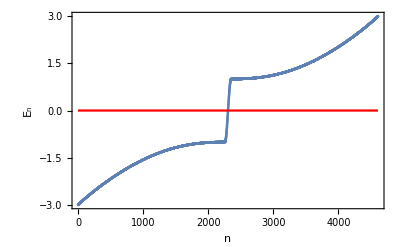

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],Plot[0,{x,0,2A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
(**----To save memory, matrices related to the above calculation for the parent crystal are deleted----**)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

4608

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+14
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+6
```

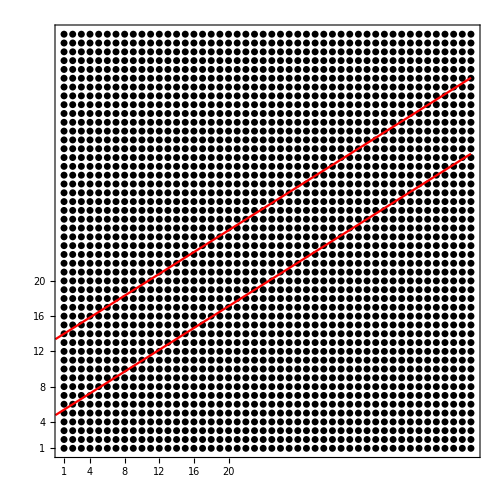

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonlist-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{241,289,290,291,337,338,339,340,341,385,386,387,388,389,390,433,434,435,436,437,438,439,440,481,482,483,484,485,486,487,488,489,490,529,530,531,532,533,534,535,536,537,538,539,577,578,579,580,581,582,583,584,585,586,587,588,589,626,627,628,629,630,631,632,633,634,635,636,637,638,675,676,677,678,679,680,681,682,683,684,685,686,687,688,725,726,727,728,729,730,731,732,733,734,735,736,737,738,774,775,776,777,778,779,780,781,782,783,784,785,786,787,824,825,826,827,828,829,830,831,832,833,834,835,836,837,874,875,876,877,878,879,880,881,882,883,884,885,886,887,923,924,925,926,927,928,929,930,931,932,933,934,935,936,973,974,975,976,977,978,979,980,981,982,983,984,985,986,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1382,1383,1419,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1469,1470,1471,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580,1581,1618,1619,1620,1621,1622,1623,1624,1625,1626,1627,1628,1629,1630,1631,1667,1668,1669,1670,1671,1672,1673,1674,1675,1676,1677,1678,1679,1680,1717,1718,1719,1720,1721,1722,1723,1724,1725,1726,1727,1728,1767,1768,1769,1770,1771,1772,1773,1774,1775,1776,1816,1817,1818,1819,1820,1821,1822,1823,1824,1866,1867,1868,1869,1870,1871,1872,1916,1917,1918,1919,1920,1965,1966,1967,1968,2015,2016,2064}

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
(**----Generate indices for the two orbitals, and group them into TotalFibon ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon]
```

{481,482,577,578,579,580,581,582,673,674,675,676,677,678,679,680,681,682,769,770,771,772,773,774,775,776,777,778,779,780,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374,1375,1376,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462,1463,1464,1465,1466,1467,1468,1469,1470,1471,1472,1473,1474,1475,1476,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1564,1565,1566,1567,1568,1569,1570,1571,1572,1573,1574,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1658,1659,1660,1661,1662,1663,1664,1665,1666,1667,1668,1669,1670,1671,1672,1673,1674,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1768,1769,1770,1771,1772,1773,1774,1845,1846,1847,1848,1849,1850,1851,1852,1853,1854,1855,1856,1857,1858,1859,1860,1861,1862,1863,1864,1865,1866,1867,1868,1869,1870,1871,1872,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,2043,2044,2045,2046,2047,2048,2049,2050,2051,2052,2053,2054,2055,2056,2057,2058,2059,2060,2061,2062,2063,2064,2065,2066,2067,2068,2069,2070,2143,2144,2145,2146,2147,2148,2149,2150,2151,2152,2153,2154,2155,2156,2157,2158,2159,2160,2161,2162,2163,2164,2165,2166,2167,2168,2169,2170,2243,2244,2245,2246,2247,2248,2249,2250,2251,2252,2253,2254,2255,2256,2257,2258,2259,2260,2261,2262,2263,2264,2265,2266,2267,2268,2269,2270,2341,2342,2343,2344,2345,2346,2347,2348,2349,2350,2351,2352,2353,2354,2355,2356,2357,2358,2359,2360,2361,2362,2363,2364,2365,2366,2367,2368,2441,2442,2443,2444,2445,2446,2447,2448,2449,2450,2451,2452,2453,2454,2455,2456,2457,2458,2459,2460,2461,2462,2463,2464,2465,2466,2467,2468,2541,2542,2543,2544,2545,2546,2547,2548,2549,2550,2551,2552,2553,2554,2555,2556,2557,2558,2559,2560,2561,2562,2563,2564,2565,2566,2639,2640,2641,2642,2643,2644,2645,2646,2647,2648,2649,2650,2651,2652,2653,2654,2655,2656,2657,2658,2659,2660,2661,2662,2663,2664,2665,2666,2739,2740,2741,2742,2743,2744,2745,2746,2747,2748,2749,2750,2751,2752,2753,2754,2755,2756,2757,2758,2759,2760,2761,2762,2763,2764,2765,2766,2837,2838,2839,2840,2841,2842,2843,2844,2845,2846,2847,2848,2849,2850,2851,2852,2853,2854,2855,2856,2857,2858,2859,2860,2861,2862,2863,2864,2937,2938,2939,2940,2941,2942,2943,2944,2945,2946,2947,2948,2949,2950,2951,2952,2953,2954,2955,2956,2957,2958,2959,2960,2961,2962,2963,2964,3037,3038,3039,3040,3041,3042,3043,3044,3045,3046,3047,3048,3049,3050,3051,3052,3053,3054,3055,3056,3057,3058,3059,3060,3061,3062,3063,3064,3135,3136,3137,3138,3139,3140,3141,3142,3143,3144,3145,3146,3147,3148,3149,3150,3151,3152,3153,3154,3155,3156,3157,3158,3159,3160,3161,3162,3235,3236,3237,3238,3239,3240,3241,3242,3243,3244,3245,3246,3247,3248,3249,3250,3251,3252,3253,3254,3255,3256,3257,3258,3259,3260,3261,3262,3333,3334,3335,3336,3337,3338,3339,3340,3341,3342,3343,3344,3345,3346,3347,3348,3349,3350,3351,3352,3353,3354,3355,3356,3357,3358,3359,3360,3433,3434,3435,3436,3437,3438,3439,3440,3441,3442,3443,3444,3445,3446,3447,3448,3449,3450,3451,3452,3453,3454,3455,3456,3533,3534,3535,3536,3537,3538,3539,3540,3541,3542,3543,3544,3545,3546,3547,3548,3549,3550,3551,3552,3631,3632,3633,3634,3635,3636,3637,3638,3639,3640,3641,3642,3643,3644,3645,3646,3647,3648,3731,3732,3733,3734,3735,3736,3737,3738,3739,3740,3741,3742,3743,3744,3831,3832,3833,3834,3835,3836,3837,3838,3839,3840,3929,3930,3931,3932,3933,3934,3935,3936,4029,4030,4031,4032,4127,4128}

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

826

```mathematica
NSitesInside = NOrbitalsQuasi/2
```

413

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

3782

```mathematica
Percentage = N[NOrbitalsQuasi/(2*A)]
```

0.179253

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{4608}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------Renormalization for  the quasicrystal-----------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianQAHI[1.,1.,-1,0.0];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
(*------------------------------------------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*-------------------------------------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon,OnlyEigenvalue]
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
(*** To save memory, I delete some matrices which are not required anymore **)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
(**-----Diagonalize the renormalized Hamiltonian-------**)
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]//Chop;
```

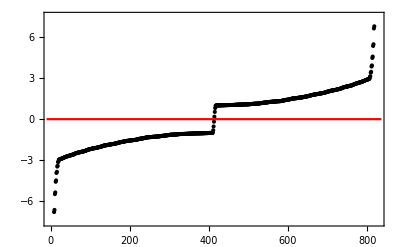

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black],Plot[0,{x,-10,NOrbitalsQuasi+10},PlotStyle-> Red]]
```

```mathematica
(** Here is the zoomed plot for energies **)
```

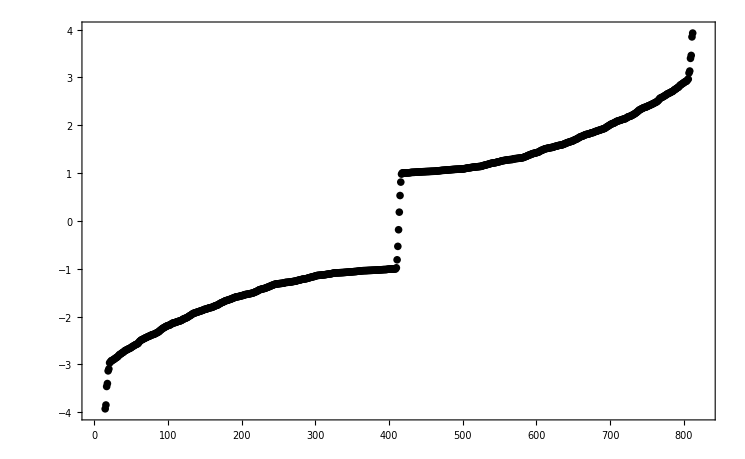

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{All,{-4,4}}]]
```

```mathematica
(** Saved plot for 48x48, for the sake of comparison **)
```

```mathematica
-Graphics-;
```

```mathematica
ValFibon;
```

```mathematica
(** Export["m=-3QuasiEnergiesPerfectLatticePBC.dat",ValFibon]; **)
```

```mathematica
OnlyEigenvalue=Table[ValFibon[[j,2]],{j,1,NOrbitalsQuasi}];
```

```mathematica
Tr[OnlyEigenvalue]//Chop
```

0

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[τ,ν,x,Fibon1D,largestX]
```

```mathematica
τ=1/D[LineUp[x],x];
ν=√(1+τ^2);
```

```mathematica
x[m_]:=m/ν+1/(τ*ν)*Round[m/τ]
```

```mathematica
Fibon1D=Table[{1+N[x[m]],0},{m,0,NOrbitalsQuasi/2}];
Dimensions[Fibon1D]
```

{414,2}

```mathematica
largestX=Ceiling[Fibon1D[[Dimensions[Fibon1D][[1]],1]]]
```

301

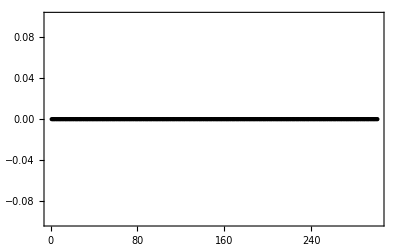

```mathematica
ListPlot[Fibon1D,Frame-> True,Axes-> False,PlotRange->{{0,largestX},{-0.1,0.1}},PlotStyle-> Black,PlotStyle->Small]
```

```mathematica
Fibon1D[[3,1]]
```

2.37638

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ValFibon[[(NOrbitalsQuasi/2)+1,2]]
```

0.183933

```mathematica
(** Put the density of the states corresponding to the two energies closest to zero in a list **)
```

```mathematica
Clear[J,TabDataFibon,TDFibon,TabFibonacci]
```

```mathematica
J=NOrbitalsQuasi/2;
```

```mathematica
TabDataFibon=Table[{Fibon1D[[i,1]],0,
Abs[ValVecFibon[[J,2,2i]]]^2+Abs[ValVecFibon[[J,2,2i-1]]]^2

+Abs[ValVecFibon[[J+1,2,2i]]]^2+Abs[ValVecFibon[[J+1,2,2i-1]]]^2

},{i,1,NOrbitalsQuasi/2}];
```

```mathematica
TDFibon=Flatten[TabDataFibon];
```

```mathematica
(** Divide the last term by 2 for normalization **)
```

```mathematica
TabFibonacci=Table[{TDFibon[[i]],TDFibon[[i+1]],TDFibon[[i+2]]/2},{i,1,3*NOrbitalsQuasi/2,3}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[colorfunc,rng,P1]
```

```mathematica
(** Red and Blue color function **)
```

```mathematica
(**colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]]; **)
```

```mathematica
(** Blur color function **)
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.2*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
(** Black and White color function **)
```

```mathematica
(** colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,0,1.0-1.0 v/vmax,v/vmax]];**)
```

```mathematica
rngOld={0,Max[#]}&@(TabFibonacci[[All,3]])
```

{0,0.0589715}

```mathematica
rng = {0,0.06}
```

{0,0.06}

```mathematica
rng[[2]]
```

0.06

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"3x10^-2"},{rng[[2]]-10^-3,"6x10^-2"}}]
```

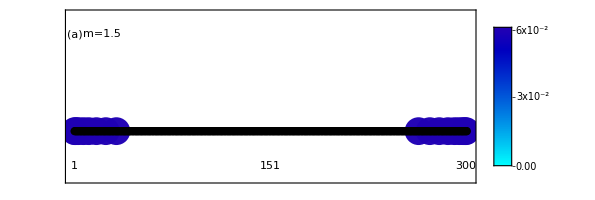

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
Frame->True,FrameTicks-> {None,None},FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,largestX+1},{-3.5,8.5}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}]
,
Epilog-> {Inset[1,{1,-2.5}],Inset[Ceiling[largestX/2],{Ceiling[largestX/2],-2.5}],Inset[largestX-1,{largestX-1,-2.5}],
Rotate[Inset[P1,{10.5,5.00}],90 Degree],Inset["m=1.5",{21.5,7}],
Inset["(a)",{1.25,7}]
}
]
```

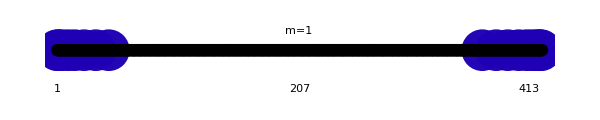

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
BaseStyle-> 18,
PlotRange-> {{-0.5,largestX+2},{-15,10}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}],
Epilog-> {Inset[1,{1,-10}],Inset[Ceiling[NSitesInside/2],{Ceiling[largestX/2],-10}],Inset[NSitesInside,{largestX-8,-10}],Inset["m=1",{largestX/2,5}]
},ImageSize-> 600
]
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```